# Лабораторная работа 14 Лабун Екатерина α = 0.3k, k = 7

```mathematica
(∂^2 u(x, y))/(∂x^2)+(∂^2 u(x, y))/(∂y^2)=(α^2+1)
```

```mathematica
α=0.3 7;
```

```mathematica
uΓ[x_, y_]:=(1-α) x^2 + α y^2+2 α;
```

```mathematica
h=0.2;
MM=Round[2/0.2]
t=0.2;
NN=Round[2/0.2]
```

10

10

```mathematica
xm=Table[h m, {m, 0, MM}]-1
yn=Table[t n , {n, 0,NN}]-1
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

```mathematica
Flatten[Outer[{#1, #2}&, xm, yn], 1];
set=Select[%, (#⟦1⟧)^2+(#⟦2⟧)^2<=1&];
```

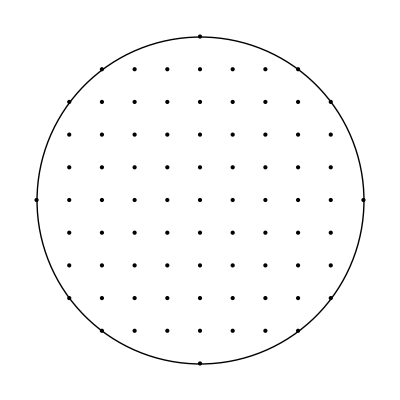

```mathematica
Graphics[{Point/@set, Circle[]}]
```

u(A)=(h u(C)+γ u(B))/(h+γ)

```mathematica
cond={
Subscript[u, {0, 5}]==uΓ[0., 1.],
Subscript[u, {5, 0}]==uΓ[1., 0.],
Subscript[u, {0, -5}]==uΓ[0., -1.],
Subscript[u, {-5, 0}]==uΓ[-1., 0.],
Subscript[u, {1, 4}]==(h uΓ[0.2, √(1-0.2^2)]+(√(1-0.2^2)-0.2 4) Subscript[u, {1, 3}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {2, 4}]==(h uΓ[0.6, 0.8]+h Subscript[u, {1, 4}])/(2h),
Subscript[u, {4, 1}]==(h uΓ[√(1-0.2^2), 0.2]+(√(1-0.2^2)-0.2 4) Subscript[u, {3,1}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {4, 2}]==(h uΓ[0.8, 0.6]+h Subscript[u, {4, 1}])/(2h),

Subscript[u, {-1, 4}]==(h uΓ[-0.2, √(1-0.2^2)]+(√(1-0.2^2)-0.2 4) Subscript[u, {-1, 3}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {-2, 4}]==(h uΓ[-0.6, 0.8]+h Subscript[u, {-1, 4}])/(2h),
Subscript[u, {-4, 1}]==(h uΓ[-√(1-0.2^2), 0.2]+(√(1-0.2^2)-0.2 4) Subscript[u, {-3,1}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {-4, 2}]==(h uΓ[-0.8, 0.6]+h Subscript[u, {-4, 1}])/(2h),

Subscript[u, {1, -4}]==(h uΓ[0.2, -√(1-0.2^2)]+(√(1-0.2^2)-0.2 4) Subscript[u, {1,- 3}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {2, -4}]==(h uΓ[0.6, -0.8]+h Subscript[u, {1, -4}])/(2h),
Subscript[u, {4, -1}]==(h uΓ[√(1-0.2^2),- 0.2]+(√(1-0.2^2)-0.2 4) Subscript[u, {3,-1}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {4, -2}]==(h uΓ[0.8, -0.6]+h Subscript[u, {4, -1}])/(2h),

Subscript[u, {-1, -4}]==(h uΓ[-0.2, -√(1-0.2^2)]+(√(1-0.2^2)-0.2 4) Subscript[u, {-1, -3}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {-2, -4}]==(h uΓ[-0.6, -0.8]+h Subscript[u, {-1, -4}])/(2h),
Subscript[u, {-4, -1}]==(h uΓ[-√(1-0.2^2),- 0.2]+(√(1-0.2^2)-0.2 4) Subscript[u, {-3,-1}])/(h+(√(1-0.2^2)-0.2 4)),
Subscript[u, {-4, -2}]==(h uΓ[-0.8, -0.6]+h Subscript[u, {-4, -1}])/(2h),

Subscript[u, {4, 3}]==uΓ[0.8, 0.6],
Subscript[u, {3, 4}]==uΓ[0.6, 0.8],
Subscript[u, {-4, 3}]==uΓ[-0.8, 0.6],
Subscript[u, {-3, 4}]==uΓ[-0.6, 0.8],
Subscript[u, {4, -3}]==uΓ[0.8, -0.6],
Subscript[u, {3, -4}]==uΓ[0.6,-0.8],
Subscript[u, {-4, -3}]==uΓ[-0.8, -0.6],
Subscript[u, {-3, -4}]==uΓ[-0.6, -0.8]
}
```

{u_{0,5}==6.3,u_{5,0}==3.1,u_{0,-5}==6.3,u_{-5,0}==3.1,u_{1,4}==2.63299 (1.2344+0.179796 u_{1,3}),u_{2,4}==2.5 (1.0296+0.2 u_{1,4}),u_{4,1}==2.63299 (0.6456+0.179796 u_{3,1}),u_{4,2}==2.5 (0.8504+0.2 u_{4,1}),u_{-1,4}==2.63299 (1.2344+0.179796 u_{-1,3}),u_{-2,4}==2.5 (1.0296+0.2 u_{-1,4}),u_{-4,1}==2.63299 (0.6456+0.179796 u_{-3,1}),u_{-4,2}==2.5 (0.8504+0.2 u_{-4,1}),u_{1,-4}==2.63299 (1.2344+0.179796 u_{1,-3}),u_{2,-4}==2.5 (1.0296+0.2 u_{1,-4}),u_{4,-1}==2.63299 (0.6456+0.179796 u_{3,-1}),u_{4,-2}==2.5 (0.8504+0.2 u_{4,-1}),u_{-1,-4}==2.63299 (1.2344+0.179796 u_{-1,-3}),u_{-2,-4}==2.5 (1.0296+0.2 u_{-1,-4}),u_{-4,-1}==2.63299 (0.6456+0.179796 u_{-3,-1}),u_{-4,-2}==2.5 (0.8504+0.2 u_{-4,-1}),u_{4,3}==4.252,u_{3,4}==5.148,u_{-4,3}==4.252,u_{-3,4}==5.148,u_{4,-3}==4.252,u_{3,-4}==5.148,u_{-4,-3}==4.252,u_{-3,-4}==5.148}

```mathematica
ui=Subscript[u, {Round[#⟦1⟧]/2, Round[#⟦2⟧]/2}]&/@(10 set);
```

```mathematica
eq=DeleteCases[Flatten[Table[If[Intersection[ui, {Subscript[u, {m+1,n}], Subscript[u, {m,n}], Subscript[u, {m-1,n}],Subscript[u, {m,n+1}], Subscript[u, {m,n-1}] }]==Sort[{Subscript[u, {m+1,n}], Subscript[u, {m,n}], Subscript[u, {m-1,n}],Subscript[u, {m,n+1}], Subscript[u, {m,n-1}]}],(Subscript[u, {m+1,n}]-2 Subscript[u, {m,n}]+Subscript[u, {m-1,n}])/h^2+(Subscript[u, {m,n+1}]-2 Subscript[u, {m,n}]+Subscript[u, {m,n-1}])/t^2==(α^2+1)], {m, -4, 4}, {n, -4, 4}], 1], Null];
```

```mathematica
Scan[Print, Join[eq, cond]]
```

25. (u_{-4,-1}-2 u_{-4,0}+u_{-4,1})+25. (u_{-5,0}-2 u_{-4,0}+u_{-3,0})==5.41

25. (u_{-3,-4}-2 u_{-3,-3}+u_{-3,-2})+25. (u_{-4,-3}-2 u_{-3,-3}+u_{-2,-3})==5.41

25. (u_{-3,-3}-2 u_{-3,-2}+u_{-3,-1})+25. (u_{-4,-2}-2 u_{-3,-2}+u_{-2,-2})==5.41

25. (u_{-3,-2}-2 u_{-3,-1}+u_{-3,0})+25. (u_{-4,-1}-2 u_{-3,-1}+u_{-2,-1})==5.41

25. (u_{-3,-1}-2 u_{-3,0}+u_{-3,1})+25. (u_{-4,0}-2 u_{-3,0}+u_{-2,0})==5.41

25. (u_{-3,0}-2 u_{-3,1}+u_{-3,2})+25. (u_{-4,1}-2 u_{-3,1}+u_{-2,1})==5.41

25. (u_{-3,1}-2 u_{-3,2}+u_{-3,3})+25. (u_{-4,2}-2 u_{-3,2}+u_{-2,2})==5.41

25. (u_{-3,2}-2 u_{-3,3}+u_{-3,4})+25. (u_{-4,3}-2 u_{-3,3}+u_{-2,3})==5.41

25. (u_{-2,-4}-2 u_{-2,-3}+u_{-2,-2})+25. (u_{-3,-3}-2 u_{-2,-3}+u_{-1,-3})==5.41

25. (u_{-2,-3}-2 u_{-2,-2}+u_{-2,-1})+25. (u_{-3,-2}-2 u_{-2,-2}+u_{-1,-2})==5.41

25. (u_{-2,-2}-2 u_{-2,-1}+u_{-2,0})+25. (u_{-3,-1}-2 u_{-2,-1}+u_{-1,-1})==5.41

25. (u_{-2,-1}-2 u_{-2,0}+u_{-2,1})+25. (u_{-3,0}-2 u_{-2,0}+u_{-1,0})==5.41

25. (u_{-2,0}-2 u_{-2,1}+u_{-2,2})+25. (u_{-3,1}-2 u_{-2,1}+u_{-1,1})==5.41

25. (u_{-2,1}-2 u_{-2,2}+u_{-2,3})+25. (u_{-3,2}-2 u_{-2,2}+u_{-1,2})==5.41

25. (u_{-2,2}-2 u_{-2,3}+u_{-2,4})+25. (u_{-3,3}-2 u_{-2,3}+u_{-1,3})==5.41

25. (u_{-1,-4}-2 u_{-1,-3}+u_{-1,-2})+25. (u_{-2,-3}-2 u_{-1,-3}+u_{0,-3})==5.41

25. (u_{-1,-3}-2 u_{-1,-2}+u_{-1,-1})+25. (u_{-2,-2}-2 u_{-1,-2}+u_{0,-2})==5.41

25. (u_{-1,-2}-2 u_{-1,-1}+u_{-1,0})+25. (u_{-2,-1}-2 u_{-1,-1}+u_{0,-1})==5.41

25. (u_{-1,-1}-2 u_{-1,0}+u_{-1,1})+25. (u_{-2,0}-2 u_{-1,0}+u_{0,0})==5.41

25. (u_{-1,0}-2 u_{-1,1}+u_{-1,2})+25. (u_{-2,1}-2 u_{-1,1}+u_{0,1})==5.41

25. (u_{-1,1}-2 u_{-1,2}+u_{-1,3})+25. (u_{-2,2}-2 u_{-1,2}+u_{0,2})==5.41

25. (u_{-1,2}-2 u_{-1,3}+u_{-1,4})+25. (u_{-2,3}-2 u_{-1,3}+u_{0,3})==5.41

25. (u_{0,-5}-2 u_{0,-4}+u_{0,-3})+25. (u_{-1,-4}-2 u_{0,-4}+u_{1,-4})==5.41

25. (u_{0,-4}-2 u_{0,-3}+u_{0,-2})+25. (u_{-1,-3}-2 u_{0,-3}+u_{1,-3})==5.41

25. (u_{0,-3}-2 u_{0,-2}+u_{0,-1})+25. (u_{-1,-2}-2 u_{0,-2}+u_{1,-2})==5.41

25. (u_{0,-2}-2 u_{0,-1}+u_{0,0})+25. (u_{-1,-1}-2 u_{0,-1}+u_{1,-1})==5.41

25. (u_{0,-1}-2 u_{0,0}+u_{0,1})+25. (u_{-1,0}-2 u_{0,0}+u_{1,0})==5.41

25. (u_{0,0}-2 u_{0,1}+u_{0,2})+25. (u_{-1,1}-2 u_{0,1}+u_{1,1})==5.41

25. (u_{0,1}-2 u_{0,2}+u_{0,3})+25. (u_{-1,2}-2 u_{0,2}+u_{1,2})==5.41

25. (u_{0,2}-2 u_{0,3}+u_{0,4})+25. (u_{-1,3}-2 u_{0,3}+u_{1,3})==5.41

25. (u_{0,3}-2 u_{0,4}+u_{0,5})+25. (u_{-1,4}-2 u_{0,4}+u_{1,4})==5.41

25. (u_{1,-4}-2 u_{1,-3}+u_{1,-2})+25. (u_{0,-3}-2 u_{1,-3}+u_{2,-3})==5.41

25. (u_{1,-3}-2 u_{1,-2}+u_{1,-1})+25. (u_{0,-2}-2 u_{1,-2}+u_{2,-2})==5.41

25. (u_{1,-2}-2 u_{1,-1}+u_{1,0})+25. (u_{0,-1}-2 u_{1,-1}+u_{2,-1})==5.41

25. (u_{1,-1}-2 u_{1,0}+u_{1,1})+25. (u_{0,0}-2 u_{1,0}+u_{2,0})==5.41

25. (u_{1,0}-2 u_{1,1}+u_{1,2})+25. (u_{0,1}-2 u_{1,1}+u_{2,1})==5.41

25. (u_{1,1}-2 u_{1,2}+u_{1,3})+25. (u_{0,2}-2 u_{1,2}+u_{2,2})==5.41

25. (u_{1,2}-2 u_{1,3}+u_{1,4})+25. (u_{0,3}-2 u_{1,3}+u_{2,3})==5.41

25. (u_{2,-4}-2 u_{2,-3}+u_{2,-2})+25. (u_{1,-3}-2 u_{2,-3}+u_{3,-3})==5.41

25. (u_{2,-3}-2 u_{2,-2}+u_{2,-1})+25. (u_{1,-2}-2 u_{2,-2}+u_{3,-2})==5.41

25. (u_{2,-2}-2 u_{2,-1}+u_{2,0})+25. (u_{1,-1}-2 u_{2,-1}+u_{3,-1})==5.41

25. (u_{2,-1}-2 u_{2,0}+u_{2,1})+25. (u_{1,0}-2 u_{2,0}+u_{3,0})==5.41

25. (u_{2,0}-2 u_{2,1}+u_{2,2})+25. (u_{1,1}-2 u_{2,1}+u_{3,1})==5.41

25. (u_{2,1}-2 u_{2,2}+u_{2,3})+25. (u_{1,2}-2 u_{2,2}+u_{3,2})==5.41

25. (u_{2,2}-2 u_{2,3}+u_{2,4})+25. (u_{1,3}-2 u_{2,3}+u_{3,3})==5.41

25. (u_{3,-4}-2 u_{3,-3}+u_{3,-2})+25. (u_{2,-3}-2 u_{3,-3}+u_{4,-3})==5.41

25. (u_{3,-3}-2 u_{3,-2}+u_{3,-1})+25. (u_{2,-2}-2 u_{3,-2}+u_{4,-2})==5.41

25. (u_{3,-2}-2 u_{3,-1}+u_{3,0})+25. (u_{2,-1}-2 u_{3,-1}+u_{4,-1})==5.41

25. (u_{3,-1}-2 u_{3,0}+u_{3,1})+25. (u_{2,0}-2 u_{3,0}+u_{4,0})==5.41

25. (u_{3,0}-2 u_{3,1}+u_{3,2})+25. (u_{2,1}-2 u_{3,1}+u_{4,1})==5.41

25. (u_{3,1}-2 u_{3,2}+u_{3,3})+25. (u_{2,2}-2 u_{3,2}+u_{4,2})==5.41

25. (u_{3,2}-2 u_{3,3}+u_{3,4})+25. (u_{2,3}-2 u_{3,3}+u_{4,3})==5.41

25. (u_{4,-1}-2 u_{4,0}+u_{4,1})+25. (u_{3,0}-2 u_{4,0}+u_{5,0})==5.41

u_{0,5}==6.3

u_{5,0}==3.1

u_{0,-5}==6.3

u_{-5,0}==3.1

u_{1,4}==2.63299 (1.2344+0.179796 u_{1,3})

u_{2,4}==2.5 (1.0296+0.2 u_{1,4})

u_{4,1}==2.63299 (0.6456+0.179796 u_{3,1})

u_{4,2}==2.5 (0.8504+0.2 u_{4,1})

u_{-1,4}==2.63299 (1.2344+0.179796 u_{-1,3})

u_{-2,4}==2.5 (1.0296+0.2 u_{-1,4})

u_{-4,1}==2.63299 (0.6456+0.179796 u_{-3,1})

u_{-4,2}==2.5 (0.8504+0.2 u_{-4,1})

u_{1,-4}==2.63299 (1.2344+0.179796 u_{1,-3})

u_{2,-4}==2.5 (1.0296+0.2 u_{1,-4})

u_{4,-1}==2.63299 (0.6456+0.179796 u_{3,-1})

u_{4,-2}==2.5 (0.8504+0.2 u_{4,-1})

u_{-1,-4}==2.63299 (1.2344+0.179796 u_{-1,-3})

u_{-2,-4}==2.5 (1.0296+0.2 u_{-1,-4})

u_{-4,-1}==2.63299 (0.6456+0.179796 u_{-3,-1})

u_{-4,-2}==2.5 (0.8504+0.2 u_{-4,-1})

u_{4,3}==4.252

u_{3,4}==5.148

u_{-4,3}==4.252

u_{-3,4}==5.148

u_{4,-3}==4.252

u_{3,-4}==5.148

u_{-4,-3}==4.252

u_{-3,-4}==5.148

```mathematica
solution=First@Solve[
Join[
eq,
cond
], Subscript[u, {Round[#⟦1⟧]/2, Round[#⟦2⟧]/2}]&/@(10 set)]
```

{u_{-5,0}→3.1,u_{-4,-3}→4.252,u_{-4,-2}→3.78596,u_{-4,-1}→3.31991,u_{-4,0}→3.20578,u_{-4,1}→3.31991,u_{-4,2}→3.78596,u_{-4,3}→4.252,u_{-3,-4}→5.148,u_{-3,-3}→4.35508,u_{-3,-2}→3.79898,u_{-3,-1}→3.42215,u_{-3,0}→3.2997,u_{-3,1}→3.42215,u_{-3,2}→3.79898,u_{-3,3}→4.35508,u_{-3,4}→5.148,u_{-2,-4}→5.26402,u_{-2,-3}→4.43773,u_{-2,-2}→3.84913,u_{-2,-1}→3.48641,u_{-2,0}→3.36511,u_{-2,1}→3.48641,u_{-2,2}→3.84913,u_{-2,3}→4.43773,u_{-2,4}→5.26402,u_{-1,-4}→5.38004,u_{-1,-3}→4.49908,u_{-1,-2}→3.88979,u_{-1,-1}→3.52565,u_{-1,0}→3.40433,u_{-1,1}→3.52565,u_{-1,2}→3.88979,u_{-1,3}→4.49908,u_{-1,4}→5.38004,u_{0,-5}→6.3,u_{0,-4}→5.33721,u_{0,-3}→4.50517,u_{0,-2}→3.90171,u_{0,-1}→3.53848,u_{0,0}→3.41731,u_{0,1}→3.53848,u_{0,2}→3.90171,u_{0,3}→4.50517,u_{0,4}→5.33721,u_{0,5}→6.3,u_{1,-4}→5.38004,u_{1,-3}→4.49908,u_{1,-2}→3.88979,u_{1,-1}→3.52565,u_{1,0}→3.40433,u_{1,1}→3.52565,u_{1,2}→3.88979,u_{1,3}→4.49908,u_{1,4}→5.38004,u_{2,-4}→5.26402,u_{2,-3}→4.43773,u_{2,-2}→3.84913,u_{2,-1}→3.48641,u_{2,0}→3.36511,u_{2,1}→3.48641,u_{2,2}→3.84913,u_{2,3}→4.43773,u_{2,4}→5.26402,u_{3,-4}→5.148,u_{3,-3}→4.35508,u_{3,-2}→3.79898,u_{3,-1}→3.42215,u_{3,0}→3.2997,u_{3,1}→3.42215,u_{3,2}→3.79898,u_{3,3}→4.35508,u_{3,4}→5.148,u_{4,-3}→4.252,u_{4,-2}→3.78596,u_{4,-1}→3.31991,u_{4,0}→3.20578,u_{4,1}→3.31991,u_{4,2}→3.78596,u_{4,3}→4.252,u_{5,0}→3.1}

```mathematica
U=Outer[{#1, #2}&, xm, yn];
```

```mathematica
U=U/.{p_, q_}:>If[p^2+q^2<=1, Subscript[u, {Round[10 p]/2, Round[10 q]/2}], ""];
```

```mathematica
U=U/.solution;
```

```mathematica
Grid[Join[{Join[{"y_i/x_i"}, Range[-1., 1., h]]},MapThread[Prepend[#2, #1]&, {Range[-1., 1., h],U}]], Spacings->{1, 2}, Frame->{{True},{True}}]
```

y_i/x_i | -1. | -0.8 | -0.6 | -0.4 | -0.2 | 0. | 0.2 | 0.4 | 0.6 | 0.8 | 1.
-1. |  |  |  |  |  | 3.1 |  |  |  |  | 
-0.8 |  |  | 4.252 | 3.78596 | 3.31991 | 3.20578 | 3.31991 | 3.78596 | 4.252 |  | 
-0.6 |  | 5.148 | 4.35508 | 3.79898 | 3.42215 | 3.2997 | 3.42215 | 3.79898 | 4.35508 | 5.148 | 
-0.4 |  | 5.26402 | 4.43773 | 3.84913 | 3.48641 | 3.36511 | 3.48641 | 3.84913 | 4.43773 | 5.26402 | 
-0.2 |  | 5.38004 | 4.49908 | 3.88979 | 3.52565 | 3.40433 | 3.52565 | 3.88979 | 4.49908 | 5.38004 | 
0. | 6.3 | 5.33721 | 4.50517 | 3.90171 | 3.53848 | 3.41731 | 3.53848 | 3.90171 | 4.50517 | 5.33721 | 6.3
0.2 |  | 5.38004 | 4.49908 | 3.88979 | 3.52565 | 3.40433 | 3.52565 | 3.88979 | 4.49908 | 5.38004 | 
0.4 |  | 5.26402 | 4.43773 | 3.84913 | 3.48641 | 3.36511 | 3.48641 | 3.84913 | 4.43773 | 5.26402 | 
0.6 |  | 5.148 | 4.35508 | 3.79898 | 3.42215 | 3.2997 | 3.42215 | 3.79898 | 4.35508 | 5.148 | 
0.8 |  |  | 4.252 | 3.78596 | 3.31991 | 3.20578 | 3.31991 | 3.78596 | 4.252 |  | 
1. |  |  |  |  |  | 3.1 |  |  |  |  |